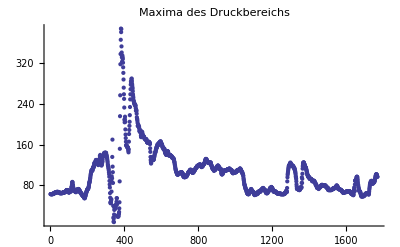

Durchschnitt des Ruhedrucks: 0.00181321

-Graphics-

c:/work/1.png

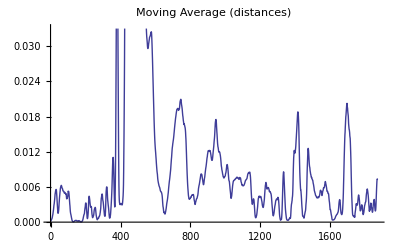

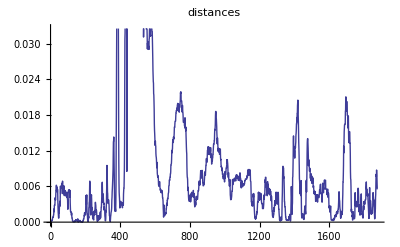

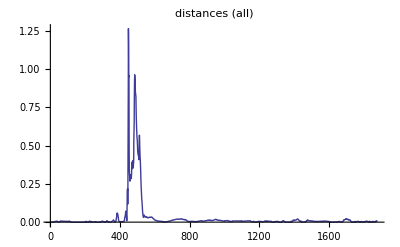

```mathematica
ClearAll[ComputeCentroids,data,data3,data2,cl2,numClusters,startIdx,endIdx,MinDist,centers,meanTrainingSet,startTraining,endTraining,schluckEndeStartPos,ruhedruck,ReadMarkers,markers,schluck];
schluck="1";
directory="M:\\Proband1\\00506534Schluck"<>schluck<>".ASC.data";
data=(Import[directory<>"\\data.csv","Data","HeaderLines"->0]);

numClusters=4;
startIdx=ToExpression[StringTake[(Import[directory<>"\\channelstart","Data","HeaderLines"->0]),{2}][[1]]];
endIdx=ToExpression[StringTake[(Import[directory<>"\\channelend","Data","HeaderLines"->0]),{2}][[1]]];

ReadMarkers[base_]:=(

start1=Import[base<>"\\rdstart","Data","HeaderLines"->0][[1]];
ende1=Import[base<>"\\rdend","Data","HeaderLines"->0][[1]];
samplerate1=Import[base<>"\\samplerate","Data","HeaderLines"->0][[1]];
start2=StringSplit[start1,":"];
start3=ToExpression[start2[[2]]]+ToExpression[start2[[1]]]*60;
ende2=StringSplit[ende1,":"];
ende3=ToExpression[ende2[[2]]]+ToExpression[ende2[[1]]]*60;
Return[{start3*ToExpression[samplerate1],ende3*ToExpression[samplerate1]}];

);

markers=ReadMarkers[directory];
startTraining=markers[[1]]-data[[1,1]];
endTraining=markers[[2]]-data[[1,1]];


ComputeCentroids[clusteringComponents_,data_,numClusters_]:=(
centers=Reap[
For[i=1,i≤numClusters,i++,(
Clear[centroid,cnt];
centroid=Table[0,{i,endIdx-startIdx+1}];

cnt=0;
For[j=1,j≤Length[data],j++,(
If[clusteringComponents[[j]]==i,(
centroid+=data[[j]];
cnt++;
)];
)]; (*of For - data*)
centroid/=cnt;
Sow[centroid,sowcentroid]
(*Print["Centroid for cluster ",i,  " is ", centroid];
Print["Sample distance: ", ToString[EuclideanDistance[data[[1]],centroid]//N]];*)

)];

,sowcentroid];
Return[Flatten[centers[[2]],1]];
);

MinDist[list_,data_]:=(
ret=100000000000000;
For[j=1,j≤Length[list],j++,(
Clear[dist];
dist=CorrelationDistance[list[[j]],data];
ret=Min[ret,dist];

)];
Return[ret];
);

(*Funktioniert aus irgend einem Grund nicht ...*)
MinDist2[l_,data_]:=(
distances=Map[CosineDistance[l,#]&,data];
distances=(CosineDistance[l,#]&)/@data;
(*Print[distances//N];*)
Return[Min[distances]];
);

FindIndex[distancesList_,startSeekIndex_,valueToFind_]:=(
l=Length[distancesList];
idx=startSeekIndex;
(*Print["Start seeking for value ",ToString[valueToFind]," from Index ",ToString[startSeekIndex]];*)
While[idx≤l,(
If[distancesList[[idx]]≤valueToFind,Return[idx]];
idx++;
)];
Return[-1];
);
MaxIdx[list_]:=(
m=Max[list];
For[j=1,j≤Length[list],j++,(
If[list[[j]]==m,(
Return[j]
)];
)];
);


data2=data[[startTraining;;endTraining,startIdx;;endIdx]];
data3=data[[All,startIdx;;endIdx]];
data4=data[[All,2;;20]];
(*
Berechnet das jeweilige Max des Sensor-bereichs über die gesamten Daten.
Ziel ist die Identifizierung des Max-Drucks in dem gesamten Bereich, von dem aus 
die Suche des Ruhedrucks starten wird.

*)
maxWindow=ParallelTable[Max[data[[i,startIdx;;endIdx]]],{i,startTraining,Length[data[[All,1]]]}];
 ListPlot[maxWindow,PlotRange->All, PlotLabel->"Maxima des Druckbereichs"] 
schluckEndeStartPos=MaxIdx[maxWindow];

(*
Clustern des Trainings-Bereichs. Der Ruhedruck wird später ermittelt, indem die Messdaten einem der Cluster am nächsten kommt.
*)
cl2=ClusteringComponents[data2,numClusters,1,DistanceFunction->CorrelationDistance,Method->"KMeans"];
centers=ComputeCentroids[cl2,data2,numClusters];
centroidList=Table[centers[[cl2[[i]]]],{i,1,Length[cl2]}];
(*,PlotStyle->{{Thick,Red},{Thick,Green}} *)

(* Die jeweilige Distanz der Messung zu den clustern (hier die minimale Distanz zu den trainings-clustern) *)
distances=ParallelMap[MinDist[centers,#]&,data3];
(*Determine mean from training set*)
meanTrainingSet=Mean[distances[[startTraining;;endTraining,All]]];
Print["Durchschnitt des Ruhedrucks: ",meanTrainingSet//N];
ruhedruck=FindIndex[distances,schluckEndeStartPos,meanTrainingSet];

daten=ListContourPlot[data3//Transpose];
marker=Graphics[{Red,Rectangle[{ruhedruck-3,1},{ruhedruck+3,endIdx-startIdx+1}]}];
markerTrainLeft=Graphics[{Green,Rectangle[{startTraining-3,1},{startTraining+3,endIdx-startIdx+1}]}];
markerTrainRight=Graphics[{Green,Rectangle[{endTraining-3,1},{endTraining+3,endIdx-startIdx+1}]}];
bild1=Show[{daten,marker,markerTrainLeft,markerTrainRight}]
(* ListPlot[Flatten[cl2,0]]*)
(* ListContourPlot[centroidList//Transpose]*)
Export["c:/work/"<>schluck<>".png",bild1]

ListPlot[MovingAverage[distances,9],Joined->True, PlotLabel->"Moving Average (distances)"]
ListPlot[distances,Joined->True,PlotLabel->"distances"]

ListPlot[distances,Joined->True,PlotRange->All, PlotLabel->"distances (all)"]
```